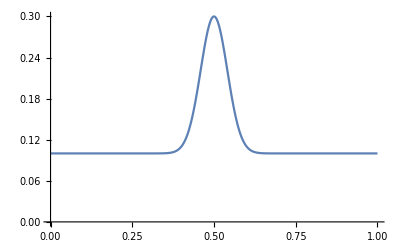

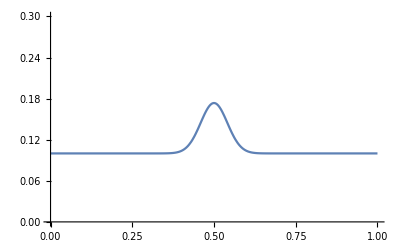

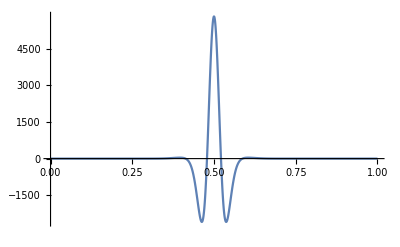

```mathematica
t0 = 0;
t1 = 0.1;
q[t_,x_]:=2/10*E^(-10t)*E^(-300(x-1/2)^2)+1/10
Plot[q[t0,x],{x,0,1},PlotRange->{{0, 1},{0, 0.3}}]
Plot[q[t1,x],{x,0,1},PlotRange->{{0, 1},{0, 0.3}}]
f[t_,x_]:=D[q[τ,ξ],τ]+D[q[τ,ξ]^3 D[q[τ,ξ],{ξ,3}],ξ]/.{τ->t,ξ->x}
Plot[f[0,x],{x,0,1},PlotRange->All]
(*D[q[t,x],t]+D[q[t,x]^2-q[t,x]^3,x]+D[q[t,x]^3 D[q[t,x],{x,3}],x]//FullSimplify
D[q[t,x],t]+D[q[t,x]^2-q[t,x]^3,x]//FullSimplify*)
```

```mathematica
D[q[t, x], t] + D[q[t,x]^2-q[t,x]^3,x]//Simplify
```

1/5 ⅇ^(-30 (t+30 (-1/2+x)^2)) (-36+ⅇ^(20 (t+30 (-1/2+x)^2)) (41-102 x)+72 x-84 ⅇ^(10 (t+30 (-1/2+x)^2)) (-1+2 x))

```mathematica
D[q[t,x],t]
```

-2 ⅇ^(-10 t-300 (-1/2+x)^2)

```mathematica
D[q[t,x]^3 D[q[t,x],{x,3}],x]
```

1/5 (1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^3 (120000 ⅇ^(-100 (-1/2+x)^2)-48000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^2+1600000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^4)-24 ⅇ^(-100 (-1/2+x)^2) (1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^2 (120000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)-8000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^3) (-1/2+x)

```mathematica
D[q[t,x],t]+D[q[t,x]^3 D[q[t,x],{x,3}],x]//Simplify
```

2 ⅇ^(-40 (t+30 (-1/2+x)^2)) (648 ⅇ^(20 (t+30 (-1/2+x)^2)) (14551-118200 x+358200 x^2-480000 x^3+240000 x^4)+1296 ⅇ^(10 (t+30 (-1/2+x)^2)) (21901-177600 x+537600 x^2-720000 x^3+360000 x^4)+864 (29251-237000 x+717000 x^2-960000 x^3+480000 x^4)+ⅇ^(30 (t+30 (-1/2+x)^2)) (777707-6350400 x+19310400 x^2-25920000 x^3+12960000 x^4))

```mathematica
D[q[t,x],t] +D[q[t,x]^2-q[t,x]^3,x]+D[q[t,x]^3 D[q[t,x],{x,3}],x]//Simplify
```

1/5 ⅇ^(-40 (t+30 (-1/2+x)^2)) (8640 (29251-237000 x+717000 x^2-960000 x^3+480000 x^4)+ⅇ^(30 (t+30 (-1/2+x)^2)) (7777121-63504102 x+193104000 x^2-259200000 x^3+129600000 x^4)+12 ⅇ^(20 (t+30 (-1/2+x)^2)) (7857547-63828014 x+193428000 x^2-259200000 x^3+129600000 x^4)+36 ⅇ^(10 (t+30 (-1/2+x)^2)) (7884359-63935998 x+193536000 x^2-259200000 x^3+129600000 x^4))

```mathematica
f[t_,x_]:=D[q[τ,ξ],τ]+D[q[τ,ξ]^3 D[q[τ,ξ],{ξ,3}],ξ]/.{τ->t,ξ->x}
```

```mathematica
Plot[f[0,x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
f[t,x]-D[q[t,x],t]-D[q[t,x]^3 D[q[t,x],{x,3}],x]
```

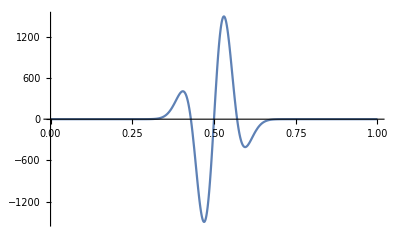

```mathematica
g[t_,x_]:=-D[q[τ,ξ]^3 D[q[τ,ξ],{ξ,3}],ξ]/.{τ->t,ξ->x}
Plot[D[q[.1,ξ],{ξ,3}]/.{ξ->x},{x,0,1},PlotRange->All]
```

```mathematica
f[t,x]//Simplify
```

2 ⅇ^(-40 (t+30 (-1/2+x)^2)) (648 ⅇ^(20 (t+30 (-1/2+x)^2)) (14551-118200 x+358200 x^2-480000 x^3+240000 x^4)+1296 ⅇ^(10 (t+30 (-1/2+x)^2)) (21901-177600 x+537600 x^2-720000 x^3+360000 x^4)+864 (29251-237000 x+717000 x^2-960000 x^3+480000 x^4)+ⅇ^(30 (t+30 (-1/2+x)^2)) (777707-6350400 x+19310400 x^2-25920000 x^3+12960000 x^4))

```mathematica
D[h[ξ]^3 D[h[ξ],{ξ,3}],ξ]
```

3 h[ξ]^2 h'[ξ] h^(3)[ξ]+h[ξ]^3 h^(4)[ξ]

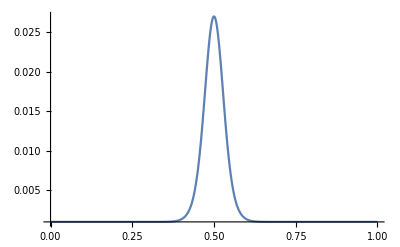

```mathematica
Plot[q[0,x]^3,{x,0,1},PlotRange->All]
```

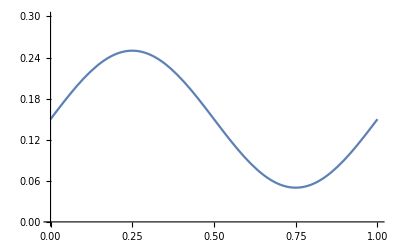

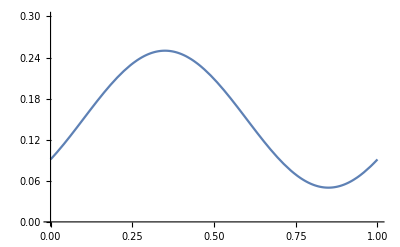

-0.628319 Cos[2 π (-t+x)]-0.467564 Cos[2 π (-t+x)]^2 (1.5+1. Sin[2 π (-t+x)])^2+0.155855 Sin[2 π (-t+x)] (1.5+1. Sin[2 π (-t+x)])^3

```mathematica
t0 = 0;
t1 = 0.1;
q[t_,x_]:=0.1*Sin[2π(x - t)]+0.15
Plot[q[t0,x],{x,0,1},PlotRange->{{0, 1},{0, 0.3}}]
Plot[q[t1,x],{x,0,1},PlotRange->{{0, 1},{0, 0.3}}]
f[t_,x_]:=D[q[τ,ξ],τ]+D[q[τ,ξ]^3 D[q[τ,ξ],{ξ,3}],ξ]/.{τ->t,ξ->x}
f[t,x]//Simplify
```

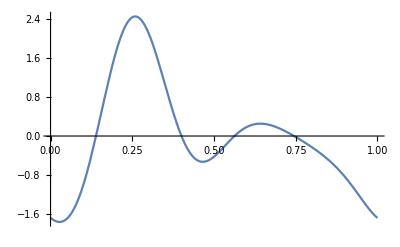

```mathematica
Plot[f[0,x],{x,0,1}]
```